# Dünne Linsen

## Funktionen

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Abbildungsgleichung(Laplace)

```mathematica
fLaplace[vg_,dvg_,vb_,dvb_]:=Module[{g,b,db,dg,f,fe},
f=1/(1/g+1/b);
fe = GError[f,{g,b},{dg,db}];
{f,fe}/.{g->vg,b->vb,dg->dvg,db->dvb}]
```

### Bessel

```mathematica
fBessel[va_,dva_,ve_,dve_] := Module[{a,e,da,de,f,fe},
f=1/4((a^2-e^2)/a);
fe= GError[f,{a,e},{da,de}];
{f,fe}/.{a->va,e->ve,da->dva,de->dve}]
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

## Laplace

### Berechnung

b ist die Position des Bildschirm
h ist die Position der Linse
g ist die Position des Gegenstandes
f ist die Brennweite der Linse

```mathematica
b = {{1115, 1136, 1087, 1011, 929, 840, 748, 656, 560, 465}} 10^-3;
db=5 10^-3;

h = {{1600, 1500, 1400, 1300, 1200, 1100, 1000, 900, 800, 700}} 10^-3;
dh = 1 10^-3;

g = {{195, 195, 195, 195, 195, 195, 195, 195, 195, 195}} 10^-2;
dg=1 10^-3;

f = fLaplace[g[[1]]-h[[1]],dg+dh,h[[1]]-b[[1]],db+dh];Grid[f//N,Frame->All]
{Mean[f[[1]]],StandardDeviation[f[[1]]]/(√Length[b[[1]]])}//N
```

0.203293 | 0.201229 | 0.199479 | 0.200053 | 0.19907 | 0.199099 | 0.199168 | 0.197991 | 0.198561 | 0.197811
0.00172893 | 0.00223363 | 0.00270008 | 0.00306451 | 0.0033785 | 0.00362811 | 0.00383582 | 0.0040217 | 0.00416655 | 0.00430135

{0.199575,0.00051741}

### Graph

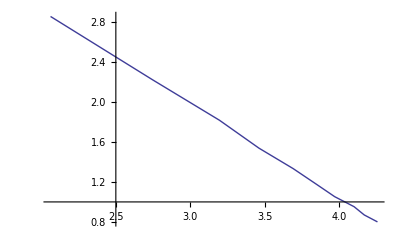

```mathematica
ListLinePlot[Table[{1/(h[[1,x]]-b[[1,x]]),1/(g[[1,x]]-h[[1,x]])},{x,1,Length[b[[1]]]}]]
```

## Bessel Verfahren

### Messung

g2 ist die Position des Gegenstandes
B2 ist die Position des Bildes
H12,H22 sind die 2 Positionen der Linse

```mathematica
g2 = {195,195,195,195,195} 10^-2;
B2 = {50,60,70,80,90} 10^-2;
H22 = {738,842,948,1056,1167} 10^-3;
H12 = {1701,1697,1691,1684,1672} 10^-3;

a2= g2-B2//N;
da2=2 10^-3;
e2= H12-H22;
de2=2 10^-3;
f2=Grid[fBessel[a2,da2,e2,de2],Frame->All]
{Mean[f2[[1,1]]],StandardDeviation[f2[[1,1]]]/(√5)}
```

0.202609 | 0.202125 | 0.20209 | 0.201764 | 0.20178
0.00138468 | 0.00133389 | 0.00127106 | 0.00119519 | 0.00109661

{0.202074,0.000153513}

## Zerstreuungslinse

### Methode 1 : ohne/mit Zerstreuung

bo3 ist Abstand von der Sammellinse zum Bild ohne Zerstreuungslinse
bm3 ist der Abstand von der Sammellinse zum Bild mit Zerstreuungslinse
lsz3 ist der Abstand der Linsen
gsz3 ist der Gegenstandsabstand für die Zerstreuungslinse

```mathematica
bo3= {928,928,928,928,928,840,840,840,840,840}10^-3;
dbo3=5 10^-3;

bm3={529,684,776,835,871,543,656,726,771,800} 10^-3;
dbm3=5 10^-3;

lz3 = {110,108,106,104,102,100,98,96,94,92}10^-2;
dlz3=10^-3;

gz3 =lz3- bo3;
dgz3 = dlz3+dbm3;

bz3 = lz3-bm3;
dbz3 = dlz3+dbm3;

f3 = fLaplace[-gz3,dgz3,bz3,dbz3] //N//MatrixForm
Mean[f3[[1,1]]]
StandardDeviation[f3[[1,1]]]/(√10)
```

(-0.246145 | -0.246689 | -0.246632 | -0.246882 | -0.240491 | -0.246195 | -0.246522 | -0.246316 | -0.244928 | -0.24
0.0134029 | 0.0181322 | 0.0254709 | 0.0378557 | 0.0566297 | 0.0159473 | 0.0220775 | 0.031928 | 0.0485961 | 0.078)

-0.24508

0.000824029

### Methode 2 : Bildpunkt der Sammellinse in den Brennpunkt der Zerstreuungslinse legen

lsz4 Abstand Sammellinse zu Zerstreuungslinse
bo4 Abstand Bild ohne Zerstreungslinse

```mathematica
lsz4 = 1;
dlsz4 = 0.1;

bo4 = 3;
dbo4 = 0.1;

f4 = bo4 - lsz4;
df4 = dbo4+lsz4;
{f4,df4}
```

{2,1.1}